```mathematica
Options@FindRoots=Sort@Join[Options@FindRoot,{MaxRecursion->Automatic,PerformanceGoal:>$PerformanceGoal,PlotPoints->Automatic,Debug->False,ZeroTolerance->10^-2}];

FindRoots[fun_,{var_,min_,max_},opts:OptionsPattern[]]:=Module[{PlotRules,RootRules,g,g2,pts,pts2,lpts,F,sol},(*Extract the Options*)PlotRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@Plot];
RootRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@FindRoot];
(*Plot the function and "mesh" the point with y-coordinate 0*)g=Normal@Plot[fun,{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros*)pts=Cases[g,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
(*Get all plot points*)lpts=Join@@Cases[g,Line[p_]:>SetPrecision[p,OptionValue@WorkingPrecision],Infinity];
(*Derive the interpolated data to find other zeros*)F=Interpolation[lpts,InterpolationOrder->2];
g2=Normal@Plot[Evaluate@D[F@var,var],{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros and retain only small ones*)pts2=Cases[g2,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
pts2=Select[pts2,Abs[F@#]<OptionValue@ZeroTolerance&];
pts=Join[pts,pts2];(*Join all zeros*)(*Refine zeros by passing each point through FindRoot*)If[Length@pts>0,pts=Map[FindRoot[fun,{var,#},Evaluate@RootRules]&,pts];
sol=Union@Select[pts,min≤Last@Last@#≤max&];
(*For debug purposes*)If[OptionValue@Debug,Print@Show[g,Graphics@{PointSize@0.02,Red,Point[{var,fun}/.sol]}]];
sol,If[OptionValue@Debug,Print@g];
{}]]
```

```mathematica
Tau0[η_,σ_,T_]:=Sum[(E^(n η)T^((σ+n)^2))/(BarnesG[1+2(σ+n)]BarnesG[1-2(σ+n)])(1+T/(2(σ+n)^2)+((8(σ+n)^2-1)T^2)/(4 (σ+n)^2(1-4 (σ+n)^2)^2)),{n,-3,3}]
TauNS[η_,a_,ℏ_,Q_]:=Sum[(E^(I n η/ℏ)(Q/ℏ^4)^(((a+I n ℏ)/ℏ)^2))/(BarnesG[1+2(a+I n ℏ)/ℏ]BarnesG[1-2(a+I n ℏ)/ℏ])(1+(Q/ℏ^4)/(2((a+I n ℏ)/ℏ)^2)+((8((a+I n ℏ)/ℏ)^2-1)(Q/ℏ^4)^2)/(4 ((a+I n ℏ)/ℏ)^2(1-4 ((a+I n ℏ)/ℏ)^2)^2)),{n,-3,3}]
TauNS2[η_,a_,ℏ_,Q_]:=Sum[(E^(I n η/ℏ)(Q/ℏ^4)^(((a+n ℏ)/ℏ)^2))/(BarnesG[1+2(a+n ℏ)/ℏ]BarnesG[1-2(a+ n ℏ)/ℏ])(1+(Q/ℏ^4)/(2((a+ n ℏ)/ℏ)^2)+((8((a+n ℏ)/ℏ)^2-1)(Q/ℏ^4)^2)/(4 ((a+ n ℏ)/ℏ)^2(1-4 ((a+ n ℏ)/ℏ)^2)^2))  ,{n,-3,3}]
```

```mathematica
h=1.5;
Q=1/13;
FindRoot[TauNS2[0, I a + h/2 ,h,Q],{a,1.2043476758428708}]
```

{a→1.20373+0. ⅈ}

```mathematica
Log[1/(2π)Cosh[2π x/.FindRoot[Abs[TauNS2[0, I a + h/2 ,h,Q]],{a,0.5},AccuracyGoal->16]]]//(NumberForm[#1,16]&)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Log[Cosh[2 π x]/(2 π)]

```mathematica
f[x_ ?NumericQ]:=Log[1+Log[1+Abs[TauNS2[0, I x + h/2 ,h,Q]]]]
Attributes[f]={Listable};
```

```mathematica
times=Range[1.2,6,.01];
vals=f[times];
```

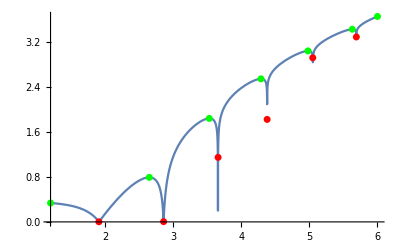

{1.91,2.86,3.66,4.38,5.05,5.69}

{9.46986,15.4389,20.4654,24.9893,29.1991,33.2203}

```mathematica
{minD,maxD}={MinDetect@vals,MaxDetect@vals};

Plot[f[x],{x,1.2,6},Epilog->{AbsolutePointSize[5],Green,Point@Pick[Transpose@{times,vals},maxD,1],Red,Point@Pick[Transpose@{times,vals},minD,1]}]
Pick[Transpose@{times,vals},minD,1][[All,1]]
Log[1/(2π)Cosh[2π x/.x->Pick[Transpose@{times,vals},minD,1][[All,1]]]]
```

{3.72759,8.21688,13.4069,19.2013,25.5404,32.3819}

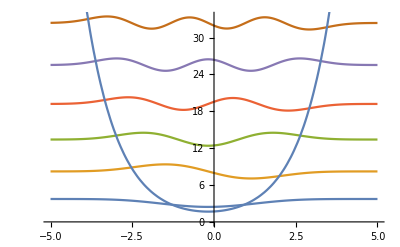

```mathematica
V[x_]:=E^x+Q E^(-x)
ℒ=-h^2*u''[x]+V[x]*u[x];
{vals,funs}=NDEigensystem[ℒ,u[x],{x,-10,100},nmax,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
vals
Show[Plot[Evaluate[Take[h*funs+vals,nmax]],{x,-5,5}],Plot[V[x],{x,-5,5}]]
```

```mathematica
Table[a^2+(Q D[Subscript[W, inst][a,h,q],q]/.q->Q),{a,{1.91,2.8600000000000003,3.66,4.38,5.05,5.69}}]
```

{3.68586,8.19869,13.4078,19.1931,25.5091,32.3813}